```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
SetOptions[Notebooks["apportionment.nb"][[1]],AutoGeneratedPackage->Automatic]
```

# Apportionment Algorithms

Every ten years, after the decennial Census, the U.S. reallocates the 435 members of Congress based on updated state populations. This has major implications for both legislation and presidential elections, since a state's electoral votes are determined the size of its delegation. Is there a better way?

## Loading the Data

While Mathematica has population conveniently built in to state entities through the Wolfram Data Repository, let's be extra careful and use the same decennial Census figures the government has used for apportionment, as well as the official number of representatives per state allotted every tens years to compare to alternate methods. This data is conveniently organized on Census.gov and gathered in `getPopulationApportionment.nb`

```mathematica
(* statesByAbbreviation = Import["./data/state_population_reps_evs.wl"]; *)
statesByAbbreviation = CloudGet["https://www.wolframcloud.com/objects/1a4bfb31-d5d4-49e3-9e04-4cf80e1fae1b"];
stateAbbrs = Keys@statesByAbbreviation;
(* We need a list of state abbreviations without DC since it is not factored into allocation -- "Taxation Without Representation!" *)
stateAbbrs50 = Select[stateAbbrs, # != "DC"&];
```

## How it works now: The Huntington-Hill method

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

"https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions""https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions"

Let's make this equation a function for a given state, getting the 2010 decennial Census data from the data we loaded and feeding it the current number of allocated seats

```mathematica
PriorityHuntingtonHill[stateAbbr_, stateReps_] := 
	1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / Sqrt[stateReps * (stateReps + 1)]
```

The allocation function will assign electoral votes according to the above formula one at a time. We're also going to explicitly pass the priority function in case we want to try a different one later, which we definitely will, and parameterize all aspects of the allocation algorithm:

To save time, we' re also going to store the priorities until we update the number of seats in a state rather than run 50 square roots 385 times.

total_ is the total number of seats to allocate, defaulting to 435

min_ is the default number of seats that every state begins with, defaulting to 1

bonus_ is the number of seats every state gets at the end of the process, after total_ is depleted. Default is 0. Setting to 2 calculates electoral votes by accounting for senators, so long as you remember to add 3 for Washington, D.C.!

priorityFunc_ is the means of determining a state's priority, defaulting to the Huntington-Hill function defined above

```mathematica
AllocateOne[reps_, priorities_, priorityFunc_:PriorityHuntingtonHill] := (
	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	updatedPriorities = priorities;
	updatedReps = reps;
	updatedReps[topPriority] += 1;
	updatedPriorities[topPriority] = priorityFunc[topPriority, updatedReps[topPriority]];
	{ updatedReps, updatedPriorities }
);

CalculateAllocations[totalBase_:435, min_:1, bonus_:0, priorityFunc_:PriorityHuntingtonHill]:= (
	total = totalBase + 50 * -bonus; (* we need to add the post-facto bonus to the total so that it doesn't count against it *)
	stateReps = AssociationThread[stateAbbrs50, ConstantArray[min, 50]];
	statePriorities = AssociationThread[stateAbbrs50, priorityFunc[#, 1]& /@ stateAbbrs50];
	While[Total@stateReps < total, { stateReps, statePriorities } = AllocateOne[stateReps, statePriorities, priorityFunc]];
	stateReps = stateReps + bonus;
	KeySort@stateReps
);
```

## Getting and mapping the effects of our calculations

We need to be able to compare our results to the real apportionment, both to check our algorithm and see how modifications change it.

Here’s a few colors we’ll be using

```mathematica
{ lightOrange, darkOrange, green, purple, lightGray } = { RGBColor["#FFA63B"], RGBColor["#FF703B"], RGBColor["#47C045"], RGBColor["#E165FA"], RGBColor["#DCDCDC"] };
```

```mathematica
houseOfRepresentatives = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["representatives"]["2010"]& /@ stateAbbrs50
];
```

```mathematica
GetDiffs[calculatedReps_] := calculatedReps - houseOfRepresentatives;
```

We're going to optionally include the ability to sort the results

```mathematica
MakeRows[calculatedReps_, sortBy_:"alpha", ascendDescend_:-1] := (
	diffs = GetDiffs[calculatedReps];
	stateKeys = Keys@houseOfRepresentatives;
	
	(* now we can sort. This is like a `Switch` statement, but a little easier to read *)
	sortRules = <|
		"alpha" -> If[ascendDescend == -1, Sort@Keys@houseOfRepresentatives, Reverse@Sort@Keys@houseOfRepresentatives],
		"actual" -> If[ascendDescend == -1, Keys[Sort@houseOfRepresentatives], Keys[Reverse@Sort@houseOfRepresentatives]],
		"yours" -> If[ascendDescend == -1, Keys[Sort@calculatedReps], Keys[Reverse@Sort@calculatedReps]],
		"delta" -> If[ascendDescend == -1, Keys[Sort@diffs], Keys[Reverse@Sort@diffs]]
	|>;

	stateNames = sortRules[sortBy];
		
	maxDiff = Max[diffs];
	maxDiff = If[maxDiff == 0, 2, maxDiff];
		
	colorScales = {
		Function[d, White], (* states, always white *)
		Function[d, Blend[Transpose[{{-10, Max[houseOfRepresentatives]}, { White, lightOrange }}], d]], (* actual house, max is 53 *)
		Function[d, Blend[Transpose[{{-10, Max[calculatedReps]}, { White, darkOrange }}], d]], (* user calculations *)
		Function[d, Blend[Transpose[{{-maxDiff, 0, maxDiff}, { green, White, purple }}], d]] (* diffs, green for losing seats, purple for gaining *)	
	};
	
	(* convert the seating data to items for grid, adding header and footer *)	
	dataAssociations = { AssociationThread[stateNames, stateNames], houseOfRepresentatives, calculatedReps, diffs };

	heightCell = 1;
	widthCell = 2;
	
	(* convert each cell to an Item for easier formatting *)
	itemizeCell[{ dataAssociation_, colorScale_ }] := Item[Style[dataAssociation[#], FontSize->12, TextAlignment->Center],
		Background->colorScale[dataAssociation[#]],
		ItemSize->{ widthCell, heightCell },
		Alignment -> Bottom]&
	/@ stateNames;
	
	itemizedRows = Map[
		itemizeCell,
		Transpose[{ dataAssociations, colorScales }]
	];
	
	totals = { "Total", Total@houseOfRepresentatives, Total@calculatedReps, Total@diffs };
	Append[itemizedRows[[#]], Item[totals[[#]], ItemSize->{2 * widthCell, heightCell}]]& /@ Range[4]
)
```

```mathematica
HorizontalGrid[calculatedReps_, perRow_:13] := (
	rows = MakeRows[calculatedReps];
	(* build rows of grids *)
	headers = Item[#, Alignment -> Right, ItemSize->{4, 1}]& /@ { "state", "actual", "yours", "delta" };
	parts = First@Partition[rows, { 4, UpTo@perRow }];
	headerRows = Map[Flatten, Transpose[{ headers, # }]& /@ parts, {2}];
	Column[Grid[#, Frame -> All, ItemSize->All, Spacings->{0.2, 0.8}]& /@ headerRows, Spacings -> -0.1]
)
```

### Okay, time to test it!

For a test case, let’s start with making sure we get the same results as we expect under current law.

```mathematica
gutCheck = CalculateAllocations[];
HorizontalGrid[gutCheck, 26]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
yours | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
delta | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
yours | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
delta | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Then we’ll try factoring in the full electoral votes in the allotment and then subtract them at the end.

```mathematica
factorInElectors = CalculateAllocations[435, 3, -2];
HorizontalGrid[factorInElectors, 26]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
yours | 1 | 6 | 3 | 9 | 59 | 6 | 4 | 2 | 29 | 14 | 2 | 3 | 2 | 19 | 9 | 3 | 5 | 5 | 9 | 8 | 2 | 14 | 7 | 8 | 3 | 2
delta | 0 | -1 | -1 | 0 | 6 | -1 | -1 | 1 | 2 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
yours | 14 | 1 | 2 | 2 | 13 | 2 | 2 | 30 | 17 | 4 | 4 | 19 | 2 | 6 | 1 | 8 | 40 | 3 | 11 | 1 | 9 | 7 | 2 | 1 | 435
delta | 1 | 0 | -1 | 0 | 1 | -1 | -2 | 3 | 1 | -1 | -1 | 1 | 0 | -1 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0

## Let’s map it too

```mathematica
MapDiffs[calculatedReps_] := (
	entityDiffs = KeyMap[statesByAbbreviation[#]["entity"]&, GetDiffs[calculatedReps]];
	green = RGBColor["#47C045"];
	purple = RGBColor["#E165FA"];
	max = Max[entityDiffs];
	max = If[max == 0, 2, max];
	
	colorScheme = Function[d, Blend[Transpose[{{-max, 0, max}, { green, White, purple }}], d]];
	
	contentinal = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["Country","UnitedStates"], ImageSize->499, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	ak = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}], ImageSize->249, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	hi = GeoRegionValuePlot[entityDiffs, GeoRange->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}], GeoRangePadding -> {Quantity[30, "Kilometers"], Quantity[50, "Kilometers"]}, ImagePadding->{{5,0},{0,0}}, GeoRangePadding -> {Scaled[0], None}, ImageSize->250, PlotLegends->None, ColorFunction->colorScheme, ColorFunctionScaling -> False];
	Column[{
		Row[{
			Column[{
				Row[{ contentinal }, ImageSize->500],
				Row[{ak,hi}, ImageSize->500]
			}],
			BarLegend[{colorScheme, {-max, max}}, LegendMarkerSize->300]
		}]
	}]
)
```

Allowing for the electors benefits the larger-population states

```mathematica
MapDiffs[factorInElectors]
```

-Graphics-
-Graphics--Graphics-
state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID | IL | IN | KS | KY
actual | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2 | 18 | 9 | 4 | 6
yours | 1 | 6 | 3 | 9 | 59 | 6 | 4 | 2 | 29 | 14 | 2 | 3 | 2 | 19 | 9 | 3 | 5
delta | 0 | -1 | -1 | 0 | 6 | -1 | -1 | 1 | 2 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | -1
state | LA | MA | MD | ME | MI | MN | MO | MS | MT | NC | ND | NE | NH | NJ | NM | NV | NY
actual | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1 | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27
yours | 5 | 9 | 8 | 2 | 14 | 7 | 8 | 3 | 2 | 14 | 1 | 2 | 2 | 13 | 2 | 2 | 30
delta | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | -1 | 0 | 1 | -1 | -2 | 3
state | OH | OK | OR | PA | RI | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual | 16 | 5 | 5 | 18 | 2 | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
yours | 17 | 4 | 4 | 19 | 2 | 6 | 1 | 8 | 40 | 3 | 11 | 1 | 9 | 7 | 2 | 1 | 435
delta | 1 | -1 | -1 | 1 | 0 | -1 | 0 | -1 | 4 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0

## Analyzing the number of people per representative

Another way to measure the effectiveness of allocation is by measuring the ratio of the population to its number of representatives. We have the population conveniently baked in to the state data, so we’ll add a bar chart to the visualization.

```mathematica
statePopulations = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50
];
totalUSPopulation = Total@statePopulations; (* won't count DC or PR since we have no reps *)
```

Function for calculating the population per representative.

```mathematica
PeoplePerRepresentative[allocation_] := (
	perRep = AssociationThread[
		stateAbbrs50,
		Round[statePopulations[#] / allocation[#] * 1.0]& /@ stateAbbrs50
	]
)
```

```mathematica
VisualizeRepresentation[allocation_, title_:""] := (
	(* data and stats *)	
	total = Total@allocation;
	ideal = Round[totalUSPopulation / total];
	ratio = PeoplePerRepresentative[allocation];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio;
	sdPrint = NumberForm[Round[sd], DigitBlock->3];	
	ratioWithUS = Append[PeoplePerRepresentative[allocation], "US" -> ideal];

	colorScale = ColorData["Rainbow", Rescale[#1, MinMax@ratio]]&;
	colorFunction = Function[v, If[v == ideal, Yellow, colorScale[v]]];		
	
	sorted = Sort@ratioWithUS;
		
	(* bar chart *)	
	chartWidth = 900;
	chartHeight = 300;
	chartAspect = chartHeight / chartWidth;
	
	allocationWithUS = Append[allocation, "US" -> "N/A"];
		
	plotLabels = {
		{ Style[title, FontSize->24, Bold] },
		{ Style[ToString@total <> " Seats", FontSize->20] },
		{ Style["Target: " <> ToString@NumberForm[ideal, DigitBlock -> 3] <> " people per representative", FontSize->14] },
		{ Style["Standard Deviation: " <> ToString[sdPrint], FontSize->14] },
		{ Item[Style["Coefficient of Variation: " <> ToString@cov, FontSize->14, Bold], Background->LightYellow, ItemSize->{Automatic,2.5}, Alignment->Center, Frame -> True] }
	};
		
	labeledData  = Labeled[sorted[#], Rotate[Style[If[# == "US", "U.S. Average", Row[{Style[#, Bold], ": ", ToString@allocationWithUS[#]}]], If[# == "US", Black, LightGray]], Pi / 2], Top]& /@ Keys@sorted;
	BarChart[
		labeledData,
		ColorFunctionScaling -> False,		
		ColorFunction -> colorFunction,
		ImageSize -> chartWidth,
		AspectRatio -> chartAspect,
		GridLines -> { None, Automatic },
		BarSpacing -> 0,
		PlotRange -> { 0, Automatic },
		PlotRangePadding -> { 0, 0 },
		PlotRange->{ Automatic, Max[sorted] * 1.1 },
		Frame -> True,
		PlotLabel -> Grid[plotLabels, Alignment->Center]
	]
)
```

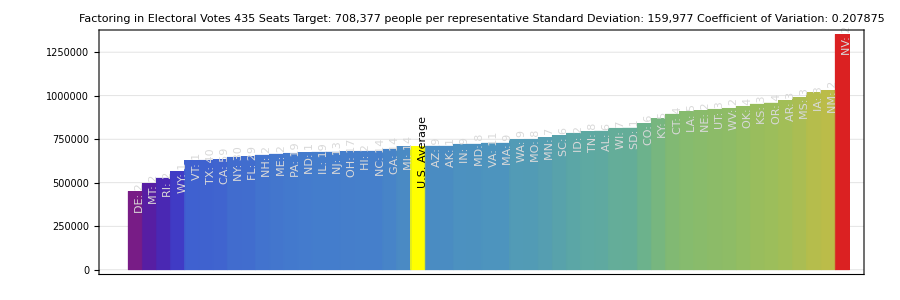

```mathematica
VisualizeRepresentation[factorInElectors, "Factoring in Electoral Votes"]
```

Let’s make that interactive and wrap this part up!

```mathematica
visualizeRepresentationInteractive = Manipulate[
	VisualizeRepresentation[CalculateAllocations[total, min, bonus, PriorityHuntingtonHill], title],
	Grid[{
		{ Control[{{title, "My Allocation", "Title:"}}], SpanFromLeft, SpanFromLeft },
		{
			Control[{{ total, 435, "Total Reps:"}, 50, 2000, 1, Appearance -> "Open" }],
			Control[{{ min, 1, "Start With:"}, 0, 40, 1, Appearance -> "Open" }],
			Control[{{ bonus, 0, "Add at End:"}, -5, 20, 1, Appearance -> "Open" }]
		}
	}, Alignment->Center],
	LabelStyle->{ FontSize -> 13 }
];
```

```mathematica
visualizeRepresentationInteractive
```

## Wrapping up

We now have all the tools we need to play with different ways to configure the House. We'll import this Notebook into a playpen and get started.